# Úkol č.2

## Jiří Krajíček Rekurze a její vliv na výpočetní složitost

Naprogramovat alespoň 3 algoritmy v Mathematice. Každý algoritmus ve dvou verzích (s rekurzí a bez rekurze).
Každý algoritmus otestovat alespoň pro různé vstupy a porovnat jejich časovou složitost. Výsledky přehledně uvést v tabulce a grafu.
Výsledný report bude obsahovat slovní závěr, ve kterém zodpovíte následující otázky:
	Jaké jsou dopady rekurze na časovou a prostorovou složitost algoritmu?

## Zdrojové kódy

```mathematica
dataExp = Table[{RandomInteger[{1,10000}],RandomInteger[{1,10000}]},5]
dataGcd = Table[{RandomInteger[{1,10000}],RandomInteger[{1,10000}]},5]
dataFib = Table[{RandomInteger[{1,30}],RandomInteger[{1,30}]},5] (*přesto, že do fibonnaciho posloupnosti je vstup pouze 1 číslo,
pro další implementaci pro vytvoření tabulky je potřeba mít o vstupní vektor navíc. Nicméně samotná funkce Fibonnaciho posloupnosti
funguje jak pro vstupní hodnotu jednoho čisla, tak pro vektor, kde si převezme pouze první hodnotu *)
```

```mathematica
(*výpočet exponentu*)
(*bez rekurze*)
expoN[x_,n_]:=Module[{i,m},
m=1;
For[i=1,i< n+1, i++,
m=m*x;
];
Return@m;
]

(*s rekurzí*)
expoR[x_,n_]:= Module[{m},
If[n==0, Return@1,
m=x*expoR[x,n-1]];
Return@m
]
```

```mathematica
(*výpočet největšího společného dělitele*)
(*bez rekurze*)
gcdN[a_,b_]:=Module[{tmp},
If[a<1||b<1,Return["error"]
];
While[b!=0,
tmp=Mod[a,b];
a=b;
b=tmp
];
Return@a
]; 

(*s rekurzí*)
gcdR[a_,b_]:=Module[{},
If[a<0||b<0,Return["error"]
];
If[a<b, Return@gcdR[b,a]
];
If[b==0, Return@a];
Return@gcdR[b,Mod[a,b]]
];
```

```mathematica
(*výpočet prvku ve Fibonnaciho posloupnosti*)
(*bez rekurze*)
(*pro mou implementaci fibonnaciho posloupnosti je možné jako vstup dát jedno celé číslo, ale stejně tak pole čísel. V takovém případě si algoritmus převezme pouze první prvek a pro něj řeší svou úlohu*)
fibN[aIa_]:=Module[{a,i,lastlast, last, result },
If[Length@aIa == 0, a=aIa, a=aIa[[1]]];
If[a==0, Return@0];
If[a==1,Return@1];
lastlast=0;
last=1;
result = 0;
For[i=1,i<a,i++,
result = lastlast + last;
lastlast=last;
last=result;
];
Return@result
];

(*s rekurzí*)
fibR[a_]:=Module[{b},
If[Length@a == 0, b=a, b=a[[1]]];
If[b==0,Return@0,
If[b==1,Return@1,Return[fibR[b-2]+fibR[b-1]]]]
];
```

## Tabulky

```mathematica
tabulka[name_,fceNonRec_,fceRec_,data_]:=Module[{results,grid},
results =Table[
Table[{d,Mean[
Table[AbsoluteTiming[f@d] [[1]],{5}]
]
}
,{d,data}]
,{f,{fceNonRec,fceRec}}
];
grid = Grid[{{name,},{"Vstup","Bez rekurze","S rekurzí"},
{results[[1]][[1]][[1]],results[[1]][[1]][[2]],results[[2]][[1]][[2]]},
{results[[1]][[2]][[1]],results[[1]][[2]][[2]],results[[2]][[2]][[2]]},
{results[[1]][[3]][[1]],results[[1]][[3]][[2]],results[[2]][[3]][[2]]},
{results[[1]][[4]][[1]],results[[1]][[4]][[2]],results[[2]][[4]][[2]]},
{results[[1]][[5]][[1]],results[[1]][[5]][[2]],results[[2]][[5]][[2]]}},
Frame->All];

Return@grid
]
(* tabulku jsem implementoval pro 5 různých výsledků k porovnání. Zároveň je funkční pro všechny
tři algoritmy*)
```

```mathematica
tabulkaExp= tabulka["Exponenciální",expoN,expoR,dataExp]
```

Exponenciální |  | 
Vstup | Bez rekurze | S rekurzí
{8270,9091} | 7.8×10^-7 | 5.4×10^-7
{5598,6600} | 9.6×10^-7 | 4.4×10^-7
{972,7574} | 4.8×10^-7 | 4.4×10^-7
{6453,4812} | 4.6×10^-7 | 4.6×10^-7
{9051,6429} | 4.6×10^-7 | 4.6×10^-7

```mathematica
tabulkaGcd= tabulka["GCD",gcdN,gcdR,dataGcd]
```

GCD |  | 
Vstup | Bez rekurze | S rekurzí
{3408,2764} | 5.6×10^-7 | 6.4×10^-7
{1010,2418} | 3.6×10^-7 | 5.6×10^-7
{2616,8628} | 4.×10^-7 | 5.4×10^-7
{845,8440} | 5.2×10^-7 | 5.×10^-7
{9179,9046} | 5.6×10^-7 | 5.×10^-7

```mathematica
tabulkaFib=tabulka["Fibonnaciho posloupnost", fibN,fibR,dataFib]
```

Fibonnaciho posloupnost |  | 
Vstup | Bez rekurze | S rekurzí
{3,30} | 0.00002696 | 0.00003152
{17,22} | 0.0000557 | 0.0324704
{12,9} | 0.00004344 | 0.0039725
{25,9} | 0.00005948 | 1.48198
{5,6} | 0.00001878 | 0.0000882

## Grafy

```mathematica
graf[name_,fceNonRec_,fceRec_,data_]:=Module[{results,input},
results =Table[
Table[{d,Mean[
Table[AbsoluteTiming[f@d] [[1]],{3}]
]
}
,{d,data}]
,{f,{fceNonRec,fceRec}}
];
input={{results[[1]][[1]][[2]],results[[1]][[2]][[2]],results[[1]][[3]][[2]],results[[1]][[4]][[2]],results[[1]][[5]][[2]]},{results[[2]][[1]][[2]],results[[2]][[2]][[2]],results[[2]][[3]][[2]],results[[2]][[4]][[2]],results[[2]][[5]][[2]]}};

ListLogPlot[input,
Joined->True,
PlotRange->All,
PlotLegends->{fceNonRec,fceRec},
PlotLabel->name,
GridLines->Automatic,
AxesLabel->{"x","y"}
]
]
```

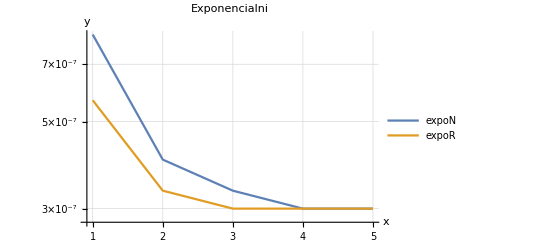

```mathematica
grafExp = graf["Exponencialni", expoN,expoR, dataExp]
```

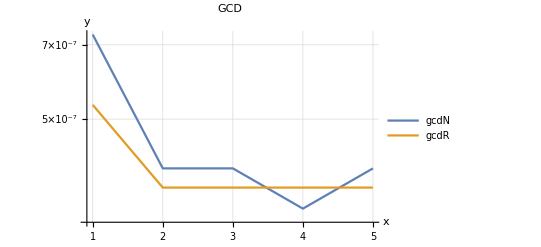

```mathematica
grafGcd = graf["GCD",gcdN,gcdR,dataGcd]
```

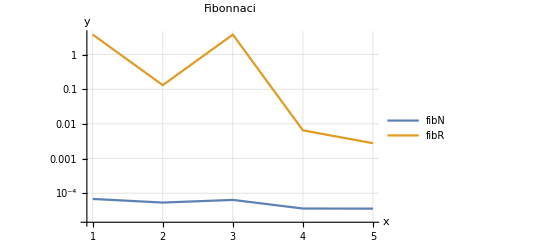

```mathematica
grafFib = graf["Fibonnaci",fibN,fibR,dataFib]
```

## Závěr

Pro tuto úlohu jsem zvolil naprogramovat algoritmus pro výpočet exponentu, největšího společného dělitele dvou čísel a prvek ve Fibonnaciho posloupnosti. Všechny z algoritmů jsem udělal jak rekurzivně, tak bez rekurze. Rekurze nám jasně dává najevo, že její prostorová složitost dokáže být úspornější. Nicméně pro některé algoritmy nemusí být časově výhodná. Největší úskalí vídím však v tom, vymyslet vlastní implementaci rekurzivního algoritmu.
	Úloha se mi moc líbila a hlavně mě seznámila s pojmem “rekurze”, který se ke me doposud nedostal. Při případných dalšíci implementacích kódů se budu dívat po rekurzivních metodách.